```mathematica
γ[t_]:=1/Sqrt[1-((xp'[t])^2+(yp'[t])^2+(zp'[t])^2)]
```

```mathematica
Z[t_]:={0,xp[t],yp[t],zp[t]}
```

```mathematica
X[t_]:={0,x,y,z}
```

```mathematica
V[t_]:=D[Z[t],t]
```

```mathematica
U[t_]:=γ[t]D[Z[t],t]
```

```mathematica
B[v_]:=({{γ[t], -γ[t]*v[[1]], -γ[t]*v[[2]], -γ[t]*v[[3]]}, {-γ[t]*v[[1]], 1+(γ[t]-1)v[[1]]^2/Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2], (γ[t]-1)(v[[1]]*v[[2]])/Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2], (γ[t]-1)(v[[1]]*v[[3]])/Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2]}, {-γ[t]*v[[2]], (γ[t]-1)(v[[1]]*v[[2]])/Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2], 1+(γ[t]-1)v[[3]]^2/Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2], (γ[t]-1)(v[[2]]*v[[3]])/Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2]}, {-γ[t]*v[[3]], (γ[t]-1)(v[[1]]*v[[3]])/Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2], (γ[t]-1)(v[[2]]*v[[3]])/Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2], 1+(γ[t]-1)v[[3]]^2/Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2]}})
```

```mathematica
Φ[x_]:=1/Sqrt[x[[2]]^2+x[[3]]^2+x[[4]]^2]
```

```mathematica
Fs[x_,z_,v_]:=Φ[B[v[[2;;4]]].(x-z)]
```

```mathematica
Φs = Fs[X[t],Z[t],V[t]]//Simplify;
```

```mathematica
Ψx=D[Φs ,x];
Ψy=D[Φs ,y];
Ψz=D[Φs ,z];
Π = D[Φs ,t];
dvΨi = D[V[t][[2]],t]D[Ψx,V[t][[2]]]+D[V[t][[3]],t]D[Ψy,V[t][[3]]]+D[V[t][[4]],t]D[Ψz,V[t][[4]]];
dvΠ = D[V[t][[2]],t]D[Π,V[t][[2]]]+D[V[t][[3]],t]D[Π,V[t][[3]]]+D[V[t][[4]],t]D[Π,V[t][[4]]];
```

```mathematica
GetPower[f0_]:=Module[{f=f0},
fs = Simplify[f/.{
xp'[t]->0.1,yp'[t]->0.0,zp'[t]->0,
xp''[t]->0.2,yp''[t]->0,zp''[t]->0,
xp[t]->0,yp[t]->0,zp[t]->0}]//FullSimplify;
    Block[{ x=r Sin[θ]Cos[φ],y = r Sin[θ]Sin[φ],z = r Cos[θ]},
Nom=Exponent[ExpandAll[Numerator[fs//Simplify]],r];
Denom=Exponent[ExpandAll[Denominator[fs//Simplify]],r];
Nom-Denom]]
```

```mathematica
GetPower[Π]
```

-1

```mathematica
GetPower[Ψx]
```

-2

```mathematica
GetPower[Φs]
```

-1

```mathematica
GetPower[dvΠ]
```

-1

```mathematica
GetPower[dvΨi]
```

-2

```mathematica
Φs/.{x->1.0, y->1.0,z->1.0,
xp'[t]->0.1,yp'[t]->0.0,zp'[t]->0.0,
(*xp''[t]->0.2,yp''[t]->0,zp''[t]->0,*)
xp[t]->5.0,yp[t]->0,zp[t]->0}
```

0.235597

```mathematica
term1=V[t][[2]] D[Fs[X[t],Z[t],V[t]],Z[t][[2]]]+V[t][[3]] D[Fs[X[t],Z[t],V[t]],Z[t][[3]]]+V[t][[4]] D[Fs[X[t],Z[t],V[t]],Z[t][[4]]];
```

```mathematica
a=D[V[t],t];
```

```mathematica
term2 = a[[2]]D[Fs[X[t],Z[t],V[t]],V[t][[2]]]+ a[[3]]D[Fs[X[t],Z[t],V[t]],V[t][[3]]]+ a[[4]]D[Fs[X[t],Z[t],V[t]],V[t][[4]]];
```

```mathematica
Π2 = term1 +  term2;
```

```mathematica
Π2/.{
x->0.1,y->0.2,z->0.3, 
xp[t]->0,yp[t]->0,zp[t]->0,
xp'[t]->0.1,yp'[t]->0.0,zp'[t]->0.0,
 xp''[t]->0.3,yp''[t]->0.0,zp''[t]->0.0}
```

0.190202

```mathematica
Π/.{
x->0.1,y->0.2,z->0.3, 
xp[t]->0,yp[t]->0,zp[t]->0,
xp'[t]->0.1,yp'[t]->0.0,zp'[t]->0.0,
 xp''[t]->0.3,yp''[t]->0.0,zp''[t]->0.0}
```

0.190202

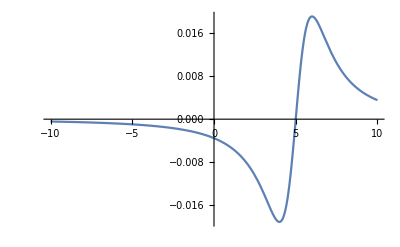

```mathematica
Plot[Π/.{x->xi, y->1.0,z->1.0,
xp'[t]->0.1,yp'[t]->0.0,zp'[t]->0,
xp''[t]->0.0,yp''[t]->0.1,zp''[t]->0,
xp[t]->5.0,yp[t]->0,zp[t]->0},{xi,-10,10},PlotRange->All]
```